Gaussian boson sampling (GBS) replaces the single photons of boson sampling with squeezed light, and the permanent with the hafnian. It is the model behind the quantum-advantage experiments Jiuzhang and Borealis. With squeezers as network elements, the quantum interferometer object  computes exact GBS amplitudes, probabilities and samples. We build GBS networks from squeezers and beam splitters, check them against the hafnian formula, and show that any pure Gaussian state is a column of squeezers followed by one interferometer. Heralded two-mode squeezed vacua recover standard boson sampling. We then test a simulated device the way the experiments do.  In a twelve-mode Jiuzhang in miniature, the torontonian predicts the clicks of threshold detectors, and loss breaks the photon pairs. Finally, encoding a graph in the squeezers makes GBS sample dense subgraphs. We also emphasize  with how the cost of a hafnian grows with the photon number to indicate a classical computer is not suitable for this problem in a larger scale.

## Introduction

A linear interferometer on m modes is a unitary transfer matrix W, with U a_k^†U^†= ∑_j W_(j k) a_j^†. In boson sampling, single photons enter the interferometer and the probability of a detection pattern is the squared permanent of a submatrix of W, which is believed to be hard to sample classically . The weak point is the source, single photons on demand are hard to make, and spontaneous parametric down-conversion emits them at random times. Gaussian boson sampling (GBS) feeds the interferometer with squeezed vacuum instead, which a nonlinear crystal produces deterministically, and the permanents become hafnians . Many photonic quantum advantage experiments  are related to GBS machines

## Paclet installation

Version 2.1.3 needed to use the QuantumInteferometer object:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
```

PacletObject[…]

Paclet loading:

```mathematica
<<Wolfram`QuantumFramework`
<<Wolfram`QuantumFramework`SecondQuantization`
```

## Squeezed vacuum: photon come in pairs

### Single mode squeezing

The single-mode squeezer is S(ξ)= exp((ξ* a^2- ξ (a^†)^2)/2) with ξ = r ⅇ^(ⅈ θ) . Its generator (a^†)^2 creates photons two at a time, so squeezed vacuum only has even photon numbers. Such that the following properties hold

Define a parametric single squeezer, in QuantumInterferometer is defined as “S”:

```mathematica
squeezer=QuantumInterferometer[{"S"[ξ]->1},1,"Parameters"->{ξ}]
```

QuantumInterferometer[…]

Photon-number distribution of the squeezed vacuum, r = 0.8, up to 10 photons:

```mathematica
squeezer[0.8]["Probabilities",{0},"Cutoff"->10]
```

<|0→0.7477,2→0.164847,4→0.0545164,6→0.0200323,8→0.00772898,10→0.00306725|>

The squeezing can also be symbolic, if we assume a real r to calculate probabilities that given an initial |0⟩ state we have k photons

For odd numbers the probabilities are zero:

```mathematica
Table[{n,FullSimplify[squeezer[r]["Probability",{0}->{2n+1}],r>0]},{n,0,7}]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0}}

Calculate it for even numbers:

```mathematica
Table[{n,Simplify[squeezer[r]["Probability",{0}->{2n}],r>0]},{n,0,7}];
```

Recover the symbolic P_(2 n)(r) with FindSequenceFunction:

```mathematica
sq0Prob = FunctionExpand@Simplify@FindSequenceFunction[%,n]
```

(n+1/2 sech(r) (tanh^2(r))^n)/(√π n+1)

Of course that distribution is normalized:

```mathematica
Simplify[∑_(n=0)^∞ sq0Prob,r>0]
```

1

And verify the mean photon number result:

```mathematica
Simplify[∑_(n=0)^∞ 2 n sq0Prob,r>0]
```

Sinh[r]^2

If the input is the single photon state |1⟩ , then only odd even Fock occupations are non zero after the squeezer

Find the P_(2n+1)(r) distribution:

```mathematica
sq1Prob=Simplify[FunctionExpand[FindSequenceFunction[Table[{n,FullSimplify[squeezer[r]["Probability",{1}->{2 n+1}],r>0]},{n,0,7}]][n]]]
```

(2 n+3/2 sech^3(r) (tanh^2(r))^n)/(√π n+1)

Check again normalization:

```mathematica
Simplify[∑_(n=0)^∞ sq1Prob,r>0]
```

1

The mean photon number also has sinh^2 behavior but with added coefficients:

```mathematica
Simplify[Sum[(2n+1)sq1Prob,{n,0,∞}],r>0]
```

3 sinh^2(r)+1

Visualize the photon distributions:

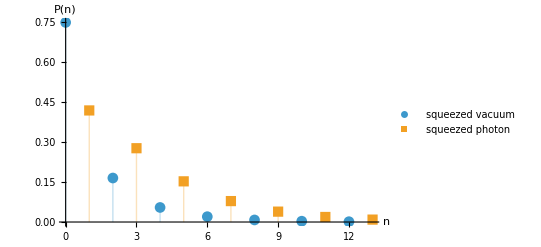

```mathematica
ListPlot[{KeyValueMap[{#1["Name"],#2}&,squeezer[0.8]["Probabilities",{0},"Cutoff"->12]],KeyValueMap[{#1["Name"],#2}&,squeezer[0.8]["Probabilities",{1},"Cutoff"->13]]},Filling->Axis,PlotMarkers->Automatic,PlotLegends->{"squeezed vacuum","squeezed photon"},AxesLabel->{"n","P(n)"},LabelStyle->13]
```

### Two mode squeezing

Two parametric squeezers with opposite signs ξ_1=r, ξ_2=r ⅇ^(ⅈ π) , combined on a 50:50 beam splitter generate a two mode squeezed vacuum

Define the parametric interferometer:

```mathematica
twoModeSqueezer=QuantumInterferometer[{"S"[r]->1,"S"[-r]->2,"BS"[π/4,0]->{1,2}},2,"Parameters"->{r}];
```

Visualize the network:

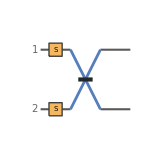

```mathematica
twoModeSqueezer["Diagram",ImageSize->150,ImagePadding->-20]
```

Calculate the non-zero patterns of the probability distribution for a given cutoff, only the |n, n⟩ patterns remain:

```mathematica
pp =DeleteCases[Simplify[#,r>0]&/@twoModeSqueezer[r]["Probabilities",{0,0},"Cutoff"->10],0]
```

<|00→Sech[r]^2,11→Sech[r]^2 Tanh[r]^2,22→Sech[r]^2 Tanh[r]^4,33→Sech[r]^2 Tanh[r]^6,44→Sech[r]^2 Tanh[r]^8,55→Sech[r]^2 Tanh[r]^10|>

The two outputs carry perfectly correlated photon numbers. Counting n photons in one arm tells us, without touching it, that the other arm holds exactly n photons. This is the state of spontaneous parametric down-conversion, and it is how heralded single-photon sources work

Compute the distribution P_(n,n)(r):

```mathematica
FindSequenceFunction[Values[pp],n+1]//Simplify
```

sech^2(r) (tanh^2(r))^n

If the squeezers are of the same sign we do not get the squeezed vacuum state:

```mathematica
sameSign=QuantumInterferometer[{"S"[1/2]->1,"S"[1/2]->2,"BS"[π/4,0]->{1,2}},2]
```

QuantumInterferometer[…]

We get other output states that are not the |n,n⟩, so it’s clear is a different state:

```mathematica
Keys[Select[sameSign[{0,0}],#!=0&]]
```

{00,20,02,40,22,04,60,42,24,06,80,62,44,26,08,100,82,64,46,28,010}

In fact the joint distribution is the product of two single-mode squeezed vacua since there are no correlations

We can clearly see that in the decomposition that the beam splitter was not doing anything:

```mathematica
sameSign["GBSForm"]["Diagram"]
```

-Graphics-

This holds for the case of using the beam-splitter with ϕ=0, in general it will depend on the relative phase of the squeezers and the ϕ of the beam-splitter

## The hafnian

The hafnian of a symmetric 2n×2n matrix is a sum over its perfect matchings, the ways to split the indices into n pairs:  Haf(A) = ∑_M Π_((i,j) ∈ M)   a_(i j). There are (2n−1)!! of them, if we expand along the first row allows to build a direct recursive definition:

Define the Hafnian:

```mathematica
hafnian[{}]:=1;
hafnian[a_]:=Sum[a[[1,j]]hafnian[a[[#,#]]&[Complement[Range[2,Length[a]],{j}]]],{j,2,Length[a]}]
```

A 4×4 symmetric matrix has three perfect matchings:

```mathematica
hafnian[Array[Subscript[b,Min[#1,#2],Max[#1,#2]]&,{4,4}]]
```

b_(1,4) b_(2,3)+b_(1,3) b_(2,4)+b_(1,2) b_(3,4)

The hafnian of the all-ones matrix counts the perfect matchings of the complete graph on 2n vertices, (2n−1)!!:

```mathematica
FindSequenceFunction[Table[hafnian[ConstantArray[1,{2n,2n}]],{n,5}],n]
```

(2 n-1)!!

For a bipartite block matrix it reduces to the permanent:

```mathematica
With[{g=Array[x,{3,3}]},Expand[hafnian[ArrayFlatten[{{0,g},{Transpose[g],0}}]]]==Expand[Permanent[g]]]
```

True

The permanent counts perfect matchings of bipartite graphs and the hafnian counts them for any graph. GBS generalizes the permanents of standard boson sampling, and the counting interpretation connects it to graph problems, as we will see at the end.

## Every pure Gaussian state is a GBS network

Squeezers and beam splitters in any order produce a Gaussian state, and with vacuum input every amplitude is a hafnian of a single symmetric matrix B

⟨n|ψ⟩ = ⟨0|ψ⟩  Haf(B_n)/√(n_1!… n_m)

The Bloch–Messiah decomposition says more any such network is an interferometer, a column of single-mode squeezers and a second interferometer. On vacuum the first interferometer does nothing, which leaves squeezers followed by one interferometer, exactly the layout of a GBS experiment

A network with squeezers in between the beam splitters:

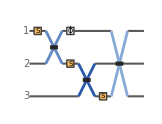

```mathematica
net=QuantumInterferometer[{"S"[0.4]->1,"BS"[0.7,0.3]->{1,2},"S"[0.3I]->2,"BS"[1.1,-0.5]->{2,3},"S"[-0.5]->3,"PS"[0.9]->1,"BS"[0.4,1.2]->{1,3}},3];
net["Diagram"]
```

Its Bloch–Messiah form, that is interferometer, squeezers, interferometer and it is exact for any input. When it can be more useful is when many squeezers are scattered through a network, it becomes at most one column of m squeezers between two passive meshes

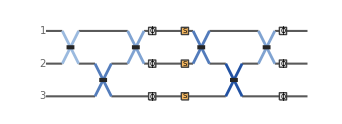

```mathematica
bm=net["BlochMessiah"];
bm["Diagram"]
```

For vacuum input, the GBS form drops the first interferometer. It takes the Takagi decomposition of B, which with our squeezer convention reads B=- W diag(tanh(r_j))Wᵀ:

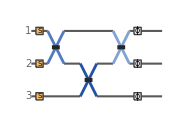

```mathematica
gbsForm=net["GBSForm"];
gbsForm["Diagram"]
```

Both forms find the same squeezing value:

```mathematica
Sort@Cases[#["Elements"],("S"[r_]->_):>r]&/@{bm,gbsForm}
```

{{0.0645869,0.295495,0.394537},{0.0645869,0.295495,0.394537}}

The Bloch–Messiah form is the same network for any input, while the GBS form is only valid for vacuum. With one photon in each of the first two modes:

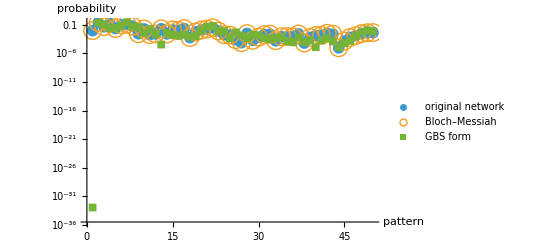

```mathematica
ListLogPlot[Values[#["Probabilities",{1,1,0},"Cutoff"->6]]&/@{net,bm,gbsForm},]
```

With vacuum input, the GBS form gives the same probabilities for every pattern up to 6 photons:

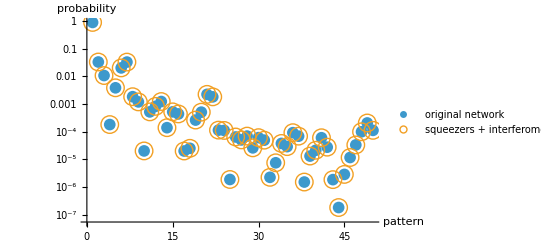

```mathematica
ListLogPlot[{Values[net["Probabilities",{0,0,0},"Cutoff"->6]],Values[gbsForm["Probabilities",{0,0,0},"Cutoff"->6]]},]
```

## Gaussian boson sampling network properties

In GBS, m squeezed vacua enter an m-mode interferometer W, and photon-number-resolving detectors record a pattern n=(n_1,… n_m). With squeezing  ξ_j= r_j ⅇ^(ⅈ ϕ_j) in mode j, the amplitude is a hafnian

-Graphics-

where B_n repeats row and column j of B  n_j times,the overall minus sign comes from our squeezer convention

A column of squeezers, ξ_j on mode j :

```mathematica
squeezers[ξs_]:=QuantumInterferometer[MapIndexed["S"[#1]->First[#2]&,ξs],Length[ξs]]
```

A GBS network is the squeezers followed by a mesh. Applying one interferometer to another places the mesh after the squeezers:

```mathematica
gbsNetwork[ξs_,mesh_]:=mesh@squeezers[ξs]
```

Four squeezers with different strengths and phases, followed by a Haar-random four-mode mesh:

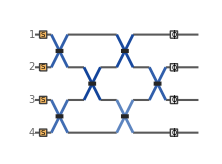

```mathematica
SeedRandom[2026];
mesh=QuantumInterferometer["Random"[4]];
ξs={0.3,0.5Exp[I π/3],0.7Exp[-I π/4],-0.4};
gbs=gbsNetwork[ξs,mesh];
gbs["Diagram"]
```

Transfer matrix of the mesh:

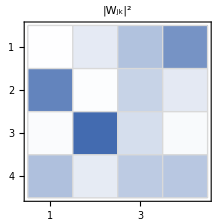
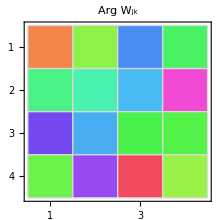

```mathematica
mesh["MatrixPlot"]
```

Indices of the photons of a pattern, mode j repeated n_j times:

```mathematica
photonIndices[n_]:=Catenate[MapIndexed[ConstantArray[First[#2],#1]&,n]]
```

The amplitude of Hamilton et al. :

```mathematica
hamiltonAmplitude[w_,ξs_,n_]:=With[{b=-w.DiagonalMatrix[Exp[ⅈ Arg[ξs]] Tanh[Abs[ξs]]].Transpose[w],idx=photonIndices[n]},hafnian[b⟦idx,idx⟧]/(√(Times@@(n!) Times@@Cosh[Abs[ξs]]))]
```

Extract the unitary:

```mathematica
w=mesh["Unitary"];
```

Every pattern up to 6 photons, 130 patterns in total:

```mathematica
patterns=Catenate[FrobeniusSolve[{1,1,1,1},#]&/@{0,2,4,6}];
Length[patterns]
```

130

Compare with QuantumInterferometer on every pattern:

```mathematica
amplitudes={gbs["Amplitude",{0,0,0,0}->#]&/@patterns,hamiltonAmplitude[w,ξs,#]&/@patterns};
```

Show the result:

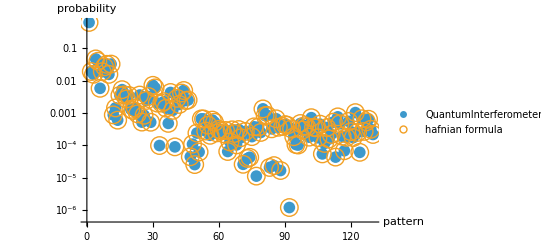

```mathematica
ListLogPlot[Abs[amplitudes]^2,PlotMarkers->{{"●",12},{"○",18}},PlotLegends->{"QuantumInterferometer","hafnian formula"},AxesLabel->{"pattern","probability"},LabelStyle->13]
```

The amplitudes, phases included, agree to machine precision:

```mathematica
Subtract@@amplitudes//Chop//Union
```

{0}

### GBS contains boson sampling

The heralded scheme of Lund et al., later called scattershot boson sampling, is a special case of GBS. Two-mode squeezed vacua feed m herald modes and m signal modes, and only the signal modes go through the interferometer. Each pair is the twoModeSqueezer  from above, on signal mode k and herald mode k+m, followed by an m-mode mesh on the signal modes:

```mathematica
scattershotNetwork[r_,mesh_]:=With[{m=mesh["Modes"]},QuantumInterferometer[Join[Catenate[Table[{"S"[r]->k,"S"[-r]->k+m,"BS"[π/4,0]->{k,k+m}},{k,m}]],mesh["Elements"]],2 m]]
```

Network squeezing parameter value:

```mathematica
rsq = 0.4;
```

Three pairs, heralds on modes 4–6, and a random three-mode mesh on the signal modes 1–3:

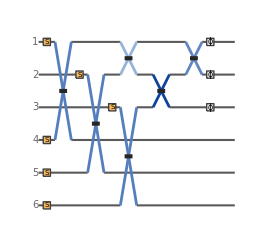

```mathematica
SeedRandom[11];
mesh3=QuantumInterferometer["Random"[3]];
scatter=scattershotNetwork[rsq,mesh3];
scatter["Diagram"]
```

Detecting the herald pattern h tells us that exactly the same pattern h of photons entered the interferometer, so the joint amplitude is a permanent, with N the number of heralded photons:

```mathematica
scattershotAmplitude[w_,r_,t_,h_]:=((-Tanh[r])^Total[h] Permanent[w⟦photonIndices[t],photonIndices[h]⟧])/(Cosh[r]^Length[h] √(Times@@(t!) Times@@(h!)))
```

Check against the permanent for several herald patterns, including one with two photons from the same source:

```mathematica
Chop@Table[scatter["Amplitude",ConstantArray[0,6]->Join[t,h]]-scattershotAmplitude[mesh3["Unitary"],rsq,t,h],{h,{{1,1,0},{1,0,1},{0,1,1},{1,1,1},{2,0,1}}},{t,FrobeniusSolve[{1,1,1},Total[h]]}]
```

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0}}

The hafnian of the full six-mode network reduces to the permanent because B is bipartite between herald and signal modes.

In the experiment the herald pattern is not chosen,  it changes from shot to shot. Sampled shots, signal modes 1–3 first and heralds 4–6 after

Sample 10^5 shots:

```mathematica
SeedRandom[5];
scatterShots=(#1["Name"]&)/@scatter["Samples",ConstantArray[0,6],10^5];
```

Every shot has as many photons in the signal modes as in the heralds:

```mathematica
AllTrue[scatterShots,Total[#[[;;3]]]==Total[#[[4;;]]]&]
```

True

The most frequent herald patterns:

```mathematica
Take[ReverseSort@Counts[scatterShots[[All,4;;]]],8]
```

<|{0,0,0}→62657,{0,1,0}→9141,{0,0,1}→8953,{1,0,0}→8919,{1,0,1}→1378,{1,1,0}→1349,{0,2,0}→1317,{2,0,0}→1316|>

Distribution of the signal pattern among the shots with herald pattern h:

```mathematica
heraldedDistribution[shots_,h_]:=Normalize[Counts[Select[shots,#[[4;;]]==h&][[All,;;3]]],Total]
```

For h = {1,1,0}, about 1300 of the shots, it is the boson sampling distribution of the mesh with one photon in modes 1 and 2 up to statistical error of the number of shots:

```mathematica
Abs/@(KeySort[heraldedDistribution[scatterShots,{1,1,0}]]-KeySort[KeyMap[#1["Name"]&,mesh3["Probabilities",{1,1,0}]]])
```

<|{0,0,2}→0.00178074,{0,1,1}→0.0042423,{0,2,0}→0.00179773,{1,0,1}→0.00114485,{1,1,0}→0.00351188,{2,0,0}→0.00532056|>

### More about photon statistics

Returning to the previously defined network:

```mathematica
gbs["Diagram"]
```

-Graphics-

Probability contained with patterns up to 12 photons:

```mathematica
probs=gbs["Probabilities",{0,0,0,0},"Cutoff"->12];
{Length[probs],Total[probs]}
```

{1036,0.999558}

Photons still come in pairs, so the total photon number is always even:

```mathematica
KeySort@Merge[KeyValueMap[Total[#1["Name"]]->#2&,probs],Total]
```

<|0→0.625203,2→0.252594,4→0.0833901,6→0.0264173,8→0.00837864,10→0.00269465,12→0.000881005|>

Passive optics conserves photon number, so the interferometer cannot change the distribution of the total photon number. That distribution is just that of the squeezers on their own. For m equal squeezers it has a closed form. With four symbolic squeezers, the probability of k pairs is (tanh(r))^(2k)/(cosh(r))^4 times (k+1):

Define the squeezers:

```mathematica
fourSqueezers=squeezers[ConstantArray[r,4]]
```

QuantumInterferometer[…]

Compute the symbolic formula:

```mathematica
FullSimplify[FindSequenceFunction[Table[{k,Total[(fourSqueezers["Probability",{0,0,0,0}->#1]&)/@FrobeniusSolve[{1,1,1,1},2 k]]},{k,0,5}],k],r>0]
```

(k+1) sech^4(r) tanh^(2 k)(r)

The total count can be classically easy to predict. Everything that makes GBS hard is in how the photons are distributed among the modes, which is what the hafnians resolve

Probabilities of the four-photon patterns:

```mathematica
fourPhotonProbabilities[qi_]:=KeySelect[qi["Probabilities",ConstantArray[0,qi["Modes"]],"Cutoff"->4],Total[#1["Name"]]==4&]
```

Show the distribution:

```mathematica
fourPhotonProbabilities[gbs]
```

<|4000→0.00252151,3100→0.00242892,3010→0.0049632,3001→0.00414891,2200→0.00184357,2110→0.00283946,2101→0.000090375,2020→0.00120951,2011→0.00431177,2002→0.000480196,1300→0.00141401,1210→0.00224271,1201→0.00201739,1120→0.000099391,1111→0.00202218,1102→0.00596433,1030→0.00717312,1021→0.000520117,1012→0.0032408,1003→0.00244692,0400→0.000854551,0310→0.000525201,0301→0.00359161,0220→0.000942739,0211→0.00141803,0202→0.00119643,0130→0.00130387,0121→0.00350767,0112→0.0027224,0103→0.00363862,0040→0.00526687,0031→0.00352494,0022→0.000603278,0013→0.00143844,0004→0.000877069|>

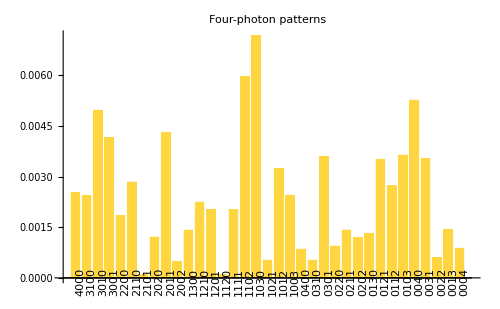

```mathematica
BarChart[Values[four],ChartLabels->Placed[Row[#["Name"]]&/@Keys[four],Below,Rotate[#,π/2]&],PlotLabel->"Four-photon patterns",ImageSize->500]
```

The collision-free pattern {1,1,1,1}  carries a small part of the four-photon probability:

```mathematica
{probs[1111],Total[four]}
```

{0.00202218,0.0833901}

With four modes there is nowhere for four photons to go without meeting. The hardness arguments assume the opposite regime, many more modes than photons . Fraction of collision-free events among the four-photon events, for a random m-mode network with equal squeezing and a mean photon number of 2:

```mathematica
collisionFreeFraction[m_,seed_]:=With[{four=fourPhotonProbabilities[gbsNetwork[ConstantArray[ArcSinh[√(2./m)],m],BlockRandom[QuantumInterferometer["Random"[m]],RandomSeeding->seed]]]},Total[KeySelect[four,Max[#["Name"]]==1&]]/Total[four]]
```

Average over three random meshes for different number of modes:

```mathematica
collisionFree=Table[{m,Mean[Table[collisionFreeFraction[m,s],{s,3}]]},{m,{4,6,8,12,16,24}}];
```

For comparison, the bosonic birthday paradox,  if all four-photon patterns were equally likely, the collision-free fraction would be Binomial[m, 4] Binomial[m+3, 4]:

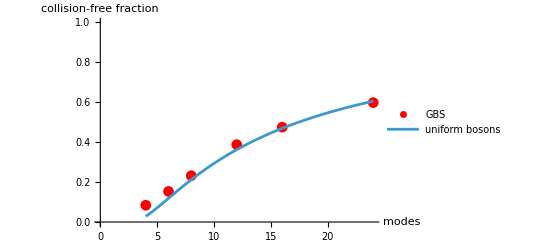

```mathematica
Show[ListPlot[collisionFree,],Plot[Binomial[m,4]/Binomial[m+3,4],{m,4,24},PlotLegends->{"uniform bosons"}]]
```

At four modes, GBS produces about three times more collision-free events than uniform bosons. Beyond eight modes the two curves are close, and the fraction approaches one half only at 16 modes, four times the photon number. Collisions become rare once the number of modes grows faster than the square of the photon number, the bosonic birthday paradox.

## Two point correlators

A device with a hundred modes cannot be checked pattern by pattern. A first test uses low-order correlations, which are easy to compute for Gaussian states. The output of the network is a Gaussian state with zero mean, fully described by N_(i j)=⟨a_i^†a_j⟩ and M_(i j)=⟨a_i a_j⟩. And by Wick’s theorem  ⟨n_i⟩ = N_(i i), cov(n_i,n_j)=|N_(i j)|^2+|M_(i j)|^2(i ≠ j)

Wick’s theorem (for bosonic operators) applies to a Gaussian state with zero mean. In such a state, the expectation of any product of creation and annihilation operators is the sum, over every way of grouping the operators into pairs, of the product of the pair expectations. With four operators there are three pairings ⟨A B C D⟩=⟨A B⟩⟨C D⟩+ ⟨A C⟩⟨B D⟩ +⟨A D⟩⟨B C⟩. Every higher moment follows from them.

For squeezed vacua in the input ⟨a_k^†a_k⟩=(sinh(r_k))^2 and ⟨a_k^2⟩=-ⅇ^(ⅈ ϕ_k)sinh(r_k)cosh(r_k):

```mathematica
secondMoments[ξs_,w_]:={Conjugate[w].DiagonalMatrix[Sinh[Abs[ξs]]^2].Transpose[w],w.DiagonalMatrix[-Exp[ⅈ Arg[ξs]] Sinh[Abs[ξs]] Cosh[Abs[ξs]]].Transpose[w]}
```

Calculate it for the GBS 4 mode network:

```mathematica
{nMat,mMat}=secondMoments[ξs,w];
```

We compare off-diagonal parts only:

```mathematica
offDiagonal[mat_]:=mat(1-IdentityMatrix[Length[mat]])
```

Largest error of the mean photon numbers and of the off-diagonal covariances of a distribution of photon counts, against Wick’s theorem:

```mathematica
wickErrors[dist_]:={Max[Abs[Mean[dist]-Re[Diagonal[nMat]]]],Max[Abs[offDiagonal[Covariance[dist]-Abs[nMat]^2-Abs[mMat]^2]]]}
```

A probability table  with each pattern weighted by its probability:

```mathematica
countDistribution[probs_]:=EmpiricalDistribution[Values[probs]->N[#["Name"]&/@Keys[probs]]]
```

Compute the cutoff dependent errors:

```mathematica
cutoffErrors=Table[Thread[{c,wickErrors[countDistribution[gbs["Probabilities",{0,0,0,0},"Cutoff"->c]]]}],{c,4,16,2}];
```

Both errors fall exponentially with the cutoff:

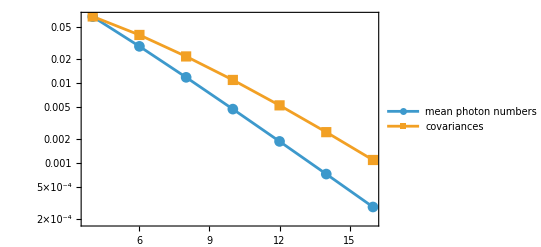

```mathematica
ListLogPlot[Transpose[cutoffErrors],Joined->True,PlotMarkers->Automatic,PlotLegends->{"mean photon numbers","covariances"},Frame->True,LabelStyle->13]
```

Sample each pattern mode by mode, heterodyne outcomes on the modes not yet counted leave the counted ones in a pure Gaussian state, and trading one heterodyne outcome at a time for a photon count gives the exact distribution

```mathematica
SeedRandom[7];
shots=(#1["Name"]&)/@gbs["Samples",{0,0,0,0},10^5];
```

Now estimate the same moments from the first k shots and measure their largest deviation from Wick’s theorem:

```mathematica
shotErrors=Table[Thread[{k,wickErrors[EmpiricalDistribution[N[shots⟦1;;k⟧]]]}],{k,Round[10^Range[2,5,0.5]]}];
```

Both deviations follow the dashed 1/√k line, the statistical error of a finite experiment, so the sampler has no bias at this level:

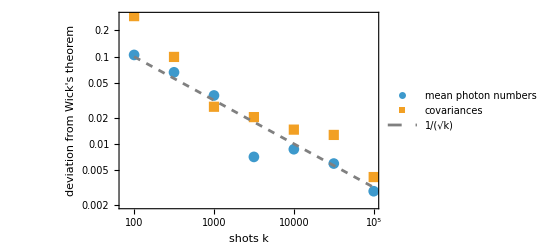

```mathematica
Show[ListLogLogPlot[Transpose[shotErrors],],LogLogPlot[1/(√k),{k,100,10^5},]]
```

The covariance has two contributions. The |N_(i j)|^2 term is the bunching that thermal light, a classical mixture of coherent states, would also show. The |M_(i j)|^2 term comes from the photon pairs. A thermal mock-up with the same N has M=0, so it predicts |N_(i j)|^2  alone. The covariance measured from all shots, for each pair of modes, against both predictions:

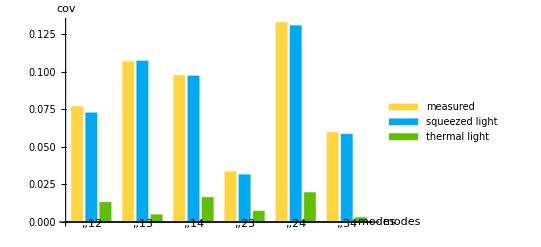

```mathematica
With[{modePairs=Subsets[Range[4],{2}]},BarChart[Transpose[{Extract[Covariance[shots],modePairs],Abs[Extract[nMat,modePairs]]^2+Abs[Extract[mMat,modePairs]]^2,Abs[Extract[nMat,modePairs]]^2}],]]
```

The thermal model falls far short because N_(i j) = ∑_k W_(i k)*W_(j k) (sinh(r_k))^2 vanishes off the diagonal when all squeezers are equal, the rows of W being orthogonal , here it only comes from the unequal squeezing. Tests like this one were used to rule out thermal and distinguishable-photon models of Jiuzhang.

## Simple model of photon loss

Loss in a mode can be described as a coupling to beam splitter with transmission η to a mode we do not look at:

```mathematica
lossySqueezer = QuantumInterferometer[{"S"[r]->1,"BS"[ArcCos[√η],0]->{1,2}},2,"Parameters"->{r,η}];
```

```mathematica
lossySqueezer["Diagram"]
```

-Graphics-

Distribution of the photons that reach the detector in mode 1:

```mathematica
detectedDistribution[r_,η_,c_]:=KeySort[Merge[KeyValueMap[#1["Name"]⟦1⟧->#2&,lossySqueezer[r,η]["Probabilities",{0,0},"Cutoff"->c]],Total]]
```

Losing one photon of a pair leaves the other one alone, so odd photon numbers appear, see the effect of loss on the photon distribution for different η:

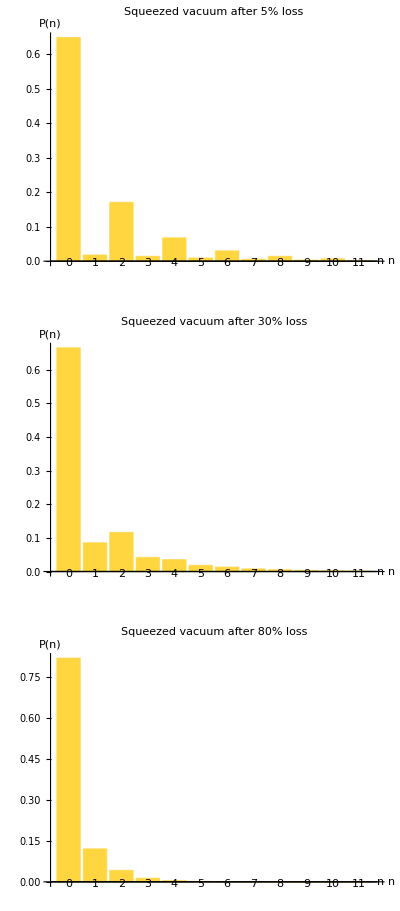

```mathematica
GraphicsColumn@Table[BarChart[Values[detectedDistribution[1.,η,50]][[;;12]],],{η,{0.95,0.7,0.2}}]
```

Calculate the distribution for r=1 , η=0.7 :

```mathematica
detected=detectedDistribution[1.,0.7,50];
```

The mean photon number is η (sinh(r))^2:

```mathematica
{Total[KeyValueMap[#1 #2&,detected]],0.7 Sinh[1.]^2}
```

{0.966764,0.966768}

For a Gaussian state the parity is  π W(0), and after loss the quadrature variances become (η ⅇ^(± 2r)+1-η)/2. This gives the probability of an odd photon number:

```mathematica
oddProbability[r_,η_]:=1/2 (1-1/(√((η Exp[2 r]+1-η) (η Exp[-2 r]+1-η))))
```

Odd fraction from the table, for transmissions from 10% to 100%:

```mathematica
oddFromTable=Table[{η,Total@KeySelect[detectedDistribution[1.,η],OddQ]},{η,0.1,1,0.1}];
```

Verify the result from the curve:

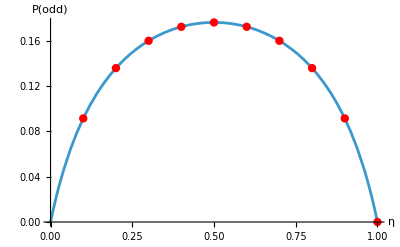

```mathematica
Show[Plot[oddProbability[1.,η],{η,0,1},],ListPlot[oddFromTable,]]
```

## Threshold detectors: Torontonians

Jiuzhang, with 50 squeezed inputs in 100 modes, used threshold detectors which only click or stay silent and recorded up to 76 clicks. The probability of a click pattern is a sum over all photon patterns with nonzero counts in the same modes. For a Gaussian state it has a closed form, the Torontonian:

where S is the set of modes that click, σ_Q is the covariance matrix of the Husimi Q function in the {a,a^†} basis, and O_Z keeps the rows and columns of the modes in Z. In terms of N and M:

```mathematica
husimiCovariance[{n_,m_}]:=With[{id=IdentityMatrix[Length[n]]},ArrayFlatten[{{Transpose[n]+id,m},{Conjugate[m],n+id}}]]
```

Since I-O_Z=(σ_Q^-1)_Z, the Torontonian only needs principal minors of σ_Q^-1:

```mathematica
clickProbability[σQ_,s_]:=With[{m=Length[σQ]/2,inv=σQ},Re[Total[((-1)^(Length[s]-Length[#1]) If[#1==={},1,1/(√Det[inv⟦Join[#1,#1+m],Join[#1,#1+m]⟧])]&)/@Subsets[s]]/(√Det[σQ])]]
```

A Jiuzhang in miniature six equal squeezers into a random twelve-mode mesh, the other six inputs left in vacuum

Define the squeezers values:

```mathematica
ξ12=PadRight[ConstantArray[0.6,6],12];
```

Build the GBS network:

```mathematica
SeedRandom[100];
jiuzhangMesh=QuantumInterferometer["Random"[12]];
jiuzhang=gbsNetwork[ξ12,jiuzhangMesh];
```

Visualize the network:

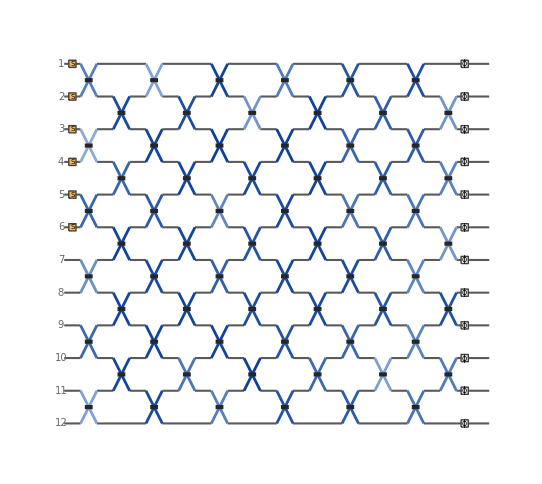

```mathematica
jiuzhang["Diagram"]
```

Compute the σ_Q:

```mathematica
σQ=husimiCovariance[secondMoments[ξ12,jiuzhangMesh["Unitary"]]];
```

The vacuum probability is 1/√(Det(σ_Q))=Π_j 1/(Cosh(r_j)):

```mathematica
Chop[{1/(√Det[σQ]),
jiuzhang["Probability",ConstantArray[0,12]->ConstantArray[0,12]],Times@@Cases[jiuzhang["Elements"],("S"[val_]->_):>1/Cosh[val]]}]
```

{0.360302,0.360302,0.360302}

A photon-number table of this network is out of reach shots carry up to 22 photons, and the table would need every pattern up to that number in twelve modes. The sampler only needs one pattern at a time:

```mathematica
SeedRandom[7];
jiuzhangShots=(#1["Name"]&)/@jiuzhang["Samples",ConstantArray[0,12],10^4];
```

Check the maximum number of photons of the shots:

```mathematica
Max[Total/@jiuzhangShots]
```

22

The Torontonian needs no cutoff it sums 2^(|S|) determinants and accounts for every photon number at once. Summed over all 4096 click patterns, it gives the distribution of the number of clicks:

```mathematica
clickCounts=GroupBy[Subsets[Range[12]],Length,Total[(clickProbability[σQ,#1]&)/@#1]&];
```

A threshold detector sees a mode with photons as one click. The same shots, counted with photon-number resolution and with threshold detectors, against the Torontonian:

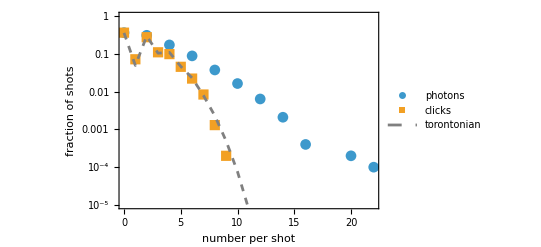

```mathematica
Show[ListLogPlot[{KeySort@Counts[Total/@jiuzhangShots],KeySort@Counts[Count[#,_?Positive]&/@jiuzhangShots]}/Length[jiuzhangShots],],ListLogPlot[clickCounts,],]
```

The clicks follow the Torontonian. The photon numbers are always even and run up to 22, while the clicks stop at 9. In twelve modes, many shots put two or more photons into the same mode, and those reach the threshold detectors as one click. When the photons spread over many more modes than there are photons, a click almost always means a single photon

Four squeezers into m modes, and the fraction of four-click events that carry exactly four photons, from the Hafnians of the collision-free patterns and the Torontonians of the same click patterns:

```mathematica
singlePhotonFraction[m_]:=Module[{mesh=QuantumInterferometer["Random"[m]],ξ=PadRight[ConstantArray[0.5,4],m],net,σ,fourClicks=Subsets[Range[m],{4}]},net=gbsNetwork[ξ,mesh];
σ=husimiCovariance[secondMoments[ξ,N[mesh["Unitary"]]]];
Total[net["Probability",ConstantArray[0,m]->Normal[SparseArray[Thread[#->1],m]]]&/@fourClicks]/Total[clickProbability[σ,#]&/@fourClicks]]
```

Calculate it  up to 24 modes in steps of 2:

```mathematica
SeedRandom[3];
fractions=Table[{m,singlePhotonFraction[m]},{m,4,24,2}];
```

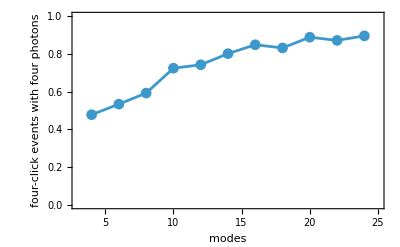

```mathematica
ListPlot[fractions,]
```

In four modes half of the four-click events carry more than four photons. In 24 modes nine in ten are clean,threshold detection approaches photon-number resolution as the modes outnumber the photons

## Graph problems: dense subgraphs and perfect matchings

For a symmetric matrix with entries 0 and 1, the adjacency matrix A of a graph, Haf(A_s) counts the perfect matchings of the subgraph with vertices S. If we can make B proportional to A, the GBS probability of the collision-free pattern on S is

P(S)=(c^(|S|)(Haf(A_S))^2)/(Π_j cosh(r_j))        where c  depends on squeezers

so the device samples subgraphs with many perfect matchings, which tend to be dense ones

A sparse random graph on 16 vertices with a complete subgraph “hidden” on six of them:

```mathematica
SeedRandom[1];
hidden=Sort@RandomSample[Range[16],6];
g=Graph[Range[16],Union[EdgeList[RandomGraph[{16,20}]],UndirectedEdge@@@Subsets[hidden,{2}]],VertexLabels->Automatic];
```

Show the subgraph:

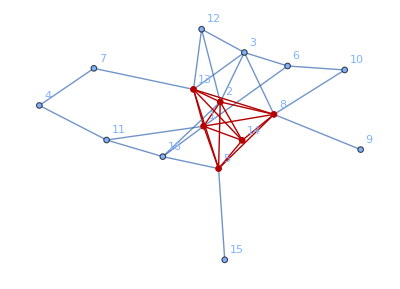

```mathematica
HighlightGraph[g,Subgraph[g,hidden]]
```

We need the Takagi decomposition A = W diag(λ)Wᵀ of the adjacency matrix itself, with W unitary and λ_j≥0 . For a real symmetric matrix the eigendecomposition is enough, multiplying the eigenvectors of negative eigenvalues by ⅈ

Extract the adjacency matrix:

```mathematica
a = AdjacencyMatrix[g];
```

Compute the eigenvalues and eigenvectors:

```mathematica
{vals,vecs}=Eigensystem[N[a]];
```

Perform the extra step for negative eigenvalues:

```mathematica
wg=Transpose[Orthogonalize[vecs]].DiagonalMatrix[ⅈ^UnitStep[-vals]];
λg=Abs[vals];
```

Check the decomposition is correct:

```mathematica
Chop[wg.DiagonalMatrix[λg].Transpose[wg]-a]
```

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

The squeezers tanh(r_j)= c λ_j , with c chosen to keep every tanh(r_j)<= 0.7:

```mathematica
c=0.7/Max[λg];
rg=ArcTanh[c λg];
```

The 0.7 was not derived from anything. It was picked it by trial as a compromise between how many six-photon events you get and how heavily one mode is squeezed.

Build the network:

```mathematica
graphGBS=gbsNetwork[rg,QuantumInterferometer[wg]];
```

The complete graph on six vertices has 5!! = 15 perfect matchings, and the probability of one photon on each hidden vertex is c^6×15^2/Π_j cosh(r_j), compared with the hafnian from the beginning of the post:

```mathematica
With[{zero=ConstantArray[0,16]},{graphGBS["Probability",zero->ReplacePart[zero,List/@hidden->1]],(c^6 hafnian[a⟦hidden,hidden⟧]^2)/(Times@@Cosh[rg]),hafnian[a⟦hidden,hidden⟧]}]
```

{0.000322267,0.000322267,15}

There are 8008 six-vertex subgraphs, and a search for the densest one has to compare them:

```mathematica
Binomial[16,6]
```

8008

We perform samples, the sampler takes about a minute and a half:

```mathematica
SeedRandom[1];
graphShots=(#1["Name"]&)/@graphGBS["Samples",ConstantArray[0,16],10^5];//EchoTiming
```

93.8736

Keep the collision-free six-photon events of 10^5 shots, each a six-vertex subgraph:

```mathematica
sixVertex=(Flatten[Position[#1,1]]&)/@Select[graphShots,Max[#1]==1&&Total[#1]==6&];
```

The hidden subgraph is the most frequent one, show the top 5:

```mathematica
Take[frequents=ReverseSort[Counts[sixVertex]],5]
```

<|{1,2,5,8,13,14}→30,{1,2,3,8,13,14}→16,{2,3,5,8,13,14}→13,{1,2,5,13,14,16}→13,{1,2,3,5,8,13}→12|>

The runners-up trade one vertex of the hidden subgraph for a well-connected neighbor:

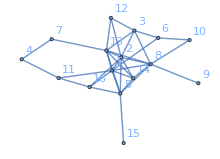
-Graphics--Graphics--Graphics-

```mathematica
Row[HighlightGraph[g,Subgraph[g,#],ImageSize->220]&/@Keys[Take[frequents,3]]]
```

Edge densities of the sampled subgraphs, against all 8008 six-vertex subgraphs drawn uniformly.  The densities you’d get by picking 6 vertices at random. In this sparse graph most have 3–5 edges:

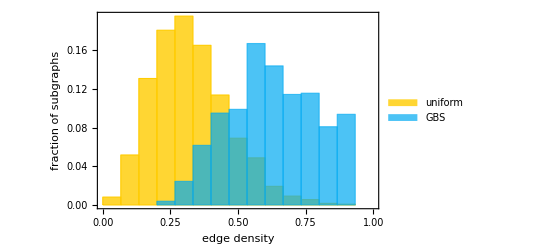

```mathematica
Histogram[{GraphDensity[Subgraph[g,#]]&/@Subsets[Range[16],{6}],GraphDensity[Subgraph[g,#]]&/@sixVertex},{0,1,1/15},]
```

The blue bars sit far to the right of the yellow ones. The device doesn’t search through the  candidates it just samples, and its samples come out much denser than random. GBS samples are good starting points for a classical search for the densest subgraph.

## How hard it gets: Complexity

Every probability needs a hafnian, and the best known algorithms for an n×n hafnian cost O(n^3 2^(n/2)) . Let’s define a 32-mode network with equal squeezing:

```mathematica
SeedRandom[3];
big=gbsNetwork[ConstantArray[0.5,32],QuantumInterferometer["Random"[32]]];
```

Photon pattern with the given occupations in the first modes:

```mathematica
onFirstModes[l_,m_]:=Join[l,ConstantArray[0,m-Length[l]]]
```

And the best of two timings of its amplitude:

```mathematica
amplitudeTiming[qi_,l_]:=Min@Table[First@AbsoluteTiming[qi["Amplitude",ConstantArray[0,qi["Modes"]]->onFirstModes[l,qi["Modes"]]]],2]
```

Time for one collision-free amplitude, as a function of the photon number:

```mathematica
times=Table[{n,amplitudeTiming[big,ConstantArray[1,n]]},{n,20,32,2}];
```

Show the complexity behavior:

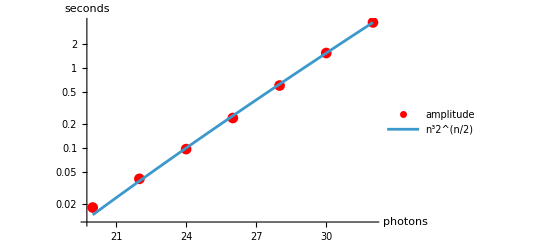

```mathematica
Show[ListLogPlot[times,],LogPlot[times⟦-1,2⟧ (n/32)^3 2^((n-32)/2),{n,20,32},]]
```

Each additional pair of photons doubles the cost, times the polynomial factor. Bunched patterns are cheaper, when row j repeats n_j times, the hafnian is a sum of  Π_j (n_j+1) , instead of 2^(n/2) for the collision-free case

With 32 photons in two modes:

```mathematica
big["Amplitude",ConstantArray[0,32]->onFirstModes[{16,16},32]];//AbsoluteTiming
```

{0.698589,Null}

Against the collision-free pattern with the same photon number:

```mathematica
big["Amplitude",ConstantArray[0,32]->onFirstModes[ConstantArray[1,32],32]];//AbsoluteTiming
```

{3.67892,Null}

For the 100×100 hafnians of a Jiuzhang-sized pattern, researchers estimated about a month and a half on a supercomputer. Better classical algorithms, exploiting loss, collisions and the structure of the experiments, can help move the boundary for quantum advantage.

## References

S. Aaronson and A. Arkhipov, The computational complexity of linear optics, Theory of Computing 9, 143–252 (2013). https://doi.org/10.4086/toc.2013.v009a004

C. S. Hamilton, R. Kruse, L. Sansoni, S. Barkhofen, C. Silberhorn and I. Jex, Gaussian Boson Sampling, Phys. Rev. Lett. 119, 170501 (2017). https://doi.org/10.1103/PhysRevLett.119.170501

R. Kruse, C. S. Hamilton, L. Sansoni, S. Barkhofen, C. Silberhorn and I. Jex, Detailed study of Gaussian boson sampling, Phys. Rev. A 100, 032326 (2019). https://doi.org/10.1103/PhysRevA.100.032326

C. C. Gerry and P. L. Knight, Introductory Quantum Optics, Cambridge University Press (2005), chapter 7.

M. S. Kim, F. A. M. de Oliveira and P. L. Knight, Properties of squeezed number states and squeezed thermal states, Phys. Rev. A 40, 2494 (1989). https://doi.org/10.1103/PhysRevA.40.2494

S. L. Braunstein, Squeezing as an irreducible resource, Phys. Rev. A 71, 055801 (2005). https://doi.org/10.1103/PhysRevA.71.055801

A. P. Lund, A. Laing, S. Rahimi-Keshari, T. Rudolph, J. L. O'Brien and T. C. Ralph, Boson sampling from a Gaussian state, Phys. Rev. Lett. 113, 100502 (2014). https://doi.org/10.1103/PhysRevLett.113.100502

S. Arkhipov and G. Kuperberg, The bosonic birthday paradox, Geometry & Topology Monographs 18, 1–7 (2012). https://arxiv.org/abs/1106.0849

D. S. Phillips, M. Walschaers, J. J. Renema, I. A. Walmsley, N. Treps and J. Sperling, Benchmarking of Gaussian boson sampling using two-point correlators, Phys. Rev. A 99, 023836 (2019). https://doi.org/10.1103/PhysRevA.99.023836

N. Quesada, J. M. Arrazola and N. Killoran, Gaussian boson sampling using threshold detectors, Phys. Rev. A 98, 062322 (2018). https://doi.org/10.1103/PhysRevA.98.062322

H. Qi, D. J. Brod, N. Quesada and R. García-Patrón, Regimes of classical simulability for noisy Gaussian boson sampling, Phys. Rev. Lett. 124, 100502 (2020). https://doi.org/10.1103/PhysRevLett.124.100502

J. M. Arrazola and T. R. Bromley, Using Gaussian boson sampling to find dense subgraphs, Phys. Rev. Lett. 121, 030503 (2018). https://doi.org/10.1103/PhysRevLett.121.030503

K. Brádler, P.-L. Dallaire-Demers, P. Rebentrost, D. Su and C. Weedbrook, Gaussian boson sampling for perfect matchings of arbitrary graphs, Phys. Rev. A 98, 032310 (2018). https://doi.org/10.1103/PhysRevA.98.032310

A. Björklund, B. Gupt and N. Quesada, A faster hafnian formula for complex matrices and its benchmarking on a supercomputer, ACM J. Exp. Algorithmics 24, 1.11 (2019). https://doi.org/10.1145/3325111

Y. Kan, From moments of sum to moments of product, J. Multivariate Anal. 99, 542–554 (2008). https://doi.org/10.1016/j.jmva.2007.01.013

H.-S. Zhong et al., Quantum computational advantage using photons, Science 370, 1460–1463 (2020). https://doi.org/10.1126/science.abe8770

L. S. Madsen et al., Quantum computational advantage with a programmable photonic processor, Nature 606, 75–81 (2022). https://doi.org/10.1038/s41586-022-04725-x

J. F. F. Bulmer et al., The boundary for quantum advantage in Gaussian boson sampling, Sci. Adv. 8, eabl9236 (2022). https://doi.org/10.1126/sciadv.abl9236

N. Quesada et al., Quadratic speed-up for simulating Gaussian boson sampling, PRX Quantum 3, 010306 (2022). https://doi.org/10.1103/PRXQuantum.3.010306

## CITE THIS NOTEBOOK

Gaussian boson sampling with QuantumInterferometer: from hafnians to a miniature Jiuzhang
by Bruno Tenorio
Wolfram Community, STAFF PICKS, November 02, 2026
https://community.wolfram.com/t/28485